```mathematica
(*Article: The Role of Direct Capital Cash Transfers Towards Poverty and Extreme Poverty Alleviation - An Omega Risk Process*)
                                                      (*Authors: Flores-Contró, José M. and Arnold, Séverine*)
```

```mathematica
(*We first clean our environment.*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Now, we calculate the value of the constants as explained in Appendix A.2.*)
```

```mathematica
Subscript[m, u][x_]:=A2(x/χ)^-b Hypergeometric2F1[b,b-c+1,b-a+1,(x/χ)^-1]
```

```mathematica
Subscript[m, l][x_]:=A3(-x/((B CT- r χ)/(r-CT)))^-d Hypergeometric2F1[d,d-f+1,d-e+1,(-x/((B CT- r χ)/(r-CT)))^-1]+A4(-x/((B CT- r χ)/(r-CT)))^-e Hypergeometric2F1[e,e-f+1,e-d+1,(-x/((B CT- r χ)/(r-CT)))^-1]
```

```mathematica
sol1:=Solve[Subscript[m, l][χ]==1/(λ+δ)(CT(B-χ)Subscript[m, l]'[χ]+λ),A3]
```

```mathematica
A3:=(λ/(δ+λ)-A4 (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)]+(A4 CT e (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/((δ+λ) (B CT-r χ))+(A4 CT e (1+e-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-d+e) (-CT+r) (δ+λ) χ^2))/((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)])/((δ+λ) (B CT-r χ))-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2))
```

```mathematica
Subscript[m, l][x_]:=A3(-x/((B CT- r χ)/(r-CT)))^-d Hypergeometric2F1[d,d-f+1,d-e+1,(-x/((B CT- r χ)/(r-CT)))^-1]+A4(-x/((B CT- r χ)/(r-CT)))^-e Hypergeometric2F1[e,e-f+1,e-d+1,(-x/((B CT- r χ)/(r-CT)))^-1]
```

```mathematica
sol2:=Solve[Subscript[m, u][B]==Subscript[m, l][B],A2]
```

```mathematica
A2:=1/Hypergeometric2F1[b,1+b-c,1-a+b,χ/B](B/χ)^b (A4 (-(B (-CT+r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/(B (-CT+r))]+((-(B (-CT+r))/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] (λ/(δ+λ)-A4 (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)]+1/((δ+λ) (B CT-r χ))A4 CT e (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)]+(A4 CT e (1+e-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-d+e) (-CT+r) (δ+λ) χ^2)))/((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)])/((δ+λ) (B CT-r χ))-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))
```

```mathematica
Subscript[m, u][x_]:=A2(x/χ)^-b Hypergeometric2F1[b,b-c+1,b-a+1,(x/χ)^-1]
```

```mathematica
sol3:=Solve[Subscript[m, u]'[B]==Subscript[m, l]'[B],A4]
```

```mathematica
A4:=((b λ (-(B (-CT+r))/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))])/(B (δ+λ) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))+(d (-CT+r) λ (-(B (-CT+r))/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))])/((δ+λ) (B CT-r χ) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))+(b (1+b-c) λ χ (-(B (-CT+r))/(B CT-r χ))^-d Hypergeometric2F1[1+b,2+b-c,2-a+b,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))])/((1-a+b) B^2 (δ+λ) Hypergeometric2F1[b,1+b-c,1-a+b,χ/B] ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))+(d (1+d-f) λ (-(B (-CT+r))/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))])/(B^2 (1+d-e) (-CT+r) (δ+λ) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2))))/(-(b (-(B (-CT+r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/(B (-CT+r))])/B-(e (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-e) Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/(B (-CT+r))])/(B CT-r χ)-(b (1+b-c) χ (-(B (-CT+r))/(B CT-r χ))^-e Hypergeometric2F1[1+b,2+b-c,2-a+b,χ/B] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/(B (-CT+r))])/((1-a+b) B^2 Hypergeometric2F1[b,1+b-c,1-a+b,χ/B])+(b (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/(B ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(CT d e (-CT+r)^2 (B-χ) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/((δ+λ) (B CT-r χ)^2 ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(b CT e (-CT+r) (B-χ) (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/(B (δ+λ) (B CT-r χ) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))+(d (-CT+r) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/((B CT-r χ) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))+(b (1+b-c) χ (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[1+b,2+b-c,2-a+b,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-a+b) B^2 Hypergeometric2F1[b,1+b-c,1-a+b,χ/B] ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(b (1+b-c) CT e (-CT+r) (B-χ) χ (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[1+b,2+b-c,2-a+b,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-a+b) B^2 (δ+λ) (B CT-r χ) Hypergeometric2F1[b,1+b-c,1-a+b,χ/B] ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(CT d e (1+d-f) (B-χ) (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/(B^2 (1+d-e) (δ+λ) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))+(d (1+d-f) (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/(B^2 (1+d-e) (-CT+r) ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(e (1+e-f) (-(B (-CT+r))/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/(B (-CT+r))])/(B^2 (1-d+e) (-CT+r))-(CT d e (1+e-f) (B-χ) (-(B (-CT+r))/(B CT-r χ))^(-1-d) (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-d+e) (δ+λ) χ^2 ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(b CT e (1+e-f) (B-χ) (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/(B (1-d+e) (-CT+r) (δ+λ) χ^2 ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(b (1+b-c) CT e (1+e-f) (B-χ) (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+b,2+b-c,2-a+b,χ/B] Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-a+b) B^2 (1-d+e) (-CT+r) (δ+λ) χ Hypergeometric2F1[b,1+b-c,1-a+b,χ/B] ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2)))-(CT d e (1+d-f) (1+e-f) (B-χ) (-(B (-CT+r))/(B CT-r χ))^-d (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ)^2 Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/(B (-CT+r))] Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/(B^2 (1+d-e) (1-d+e) (-CT+r)^2 (δ+λ) χ^2 ((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-1/((δ+λ) (B CT-r χ))CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2))))
```

```mathematica
Subscript[m, l][x_]:=A3(-x/((B CT- r χ)/(r-CT)))^-d Hypergeometric2F1[d,d-f+1,d-e+1,(-x/((B CT- r χ)/(r-CT)))^-1]+A4(-x/((B CT- r χ)/(r-CT)))^-e Hypergeometric2F1[e,e-f+1,e-d+1,(-x/((B CT- r χ)/(r-CT)))^-1]
```

```mathematica
A2:=1/Hypergeometric2F1[b,1+b-c,1-a+b,χ/B](B/χ)^b (A4 (-(B (-CT+r))/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/(B (-CT+r))]+((-(B (-CT+r))/(B CT-r χ))^-d (((CT-r) χ)/(B CT-r χ))^d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/(B (-CT+r))] (λ χ+(((CT-r) χ)/(B CT-r χ))^-e (-A4 (δ+λ) χ Hypergeometric2F1[e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)]+A4 CT e (-B+χ) Hypergeometric2F1[1+e,1+e-f,1-d+e,(B CT-r χ)/(CT χ-r χ)])))/((δ+λ) χ Hypergeometric2F1[d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]+CT d (B-χ) Hypergeometric2F1[1+d,1+d-f,1+d-e,(B CT-r χ)/(CT χ-r χ)]))
```

```mathematica
A3:=(λ/(δ+λ)-A4 (-((-CT+r) χ)/(B CT-r χ))^-e Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)]+(A4 CT e (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-e) Hypergeometric2F1[e,1+e-f,1-d+e,-(B CT-r χ)/((-CT+r) χ)])/((δ+λ) (B CT-r χ))+(A4 CT e (1+e-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-e (B CT-r χ) Hypergeometric2F1[1+e,2+e-f,2-d+e,-(B CT-r χ)/((-CT+r) χ)])/((1-d+e) (-CT+r) (δ+λ) χ^2))/((-((-CT+r) χ)/(B CT-r χ))^-d Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)]-(CT d (-CT+r) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^(-1-d) Hypergeometric2F1[d,1+d-f,1+d-e,-(B CT-r χ)/((-CT+r) χ)])/((δ+λ) (B CT-r χ))-(CT d (1+d-f) (B-χ) (-((-CT+r) χ)/(B CT-r χ))^-d (B CT-r χ) Hypergeometric2F1[1+d,2+d-f,2+d-e,-(B CT-r χ)/((-CT+r) χ)])/((1+d-e) (-CT+r) (δ+λ) χ^2))
```

```mathematica
Subscript[m, u][x_]:=A2(x/χ)^-b Hypergeometric2F1[b,b-c+1,b-a+1,(x/χ)^-1]
```

```mathematica
(*Once we have calculated the value of the constants, we can then define our piecewise function: TrappingProbability (This is formula (3.10) in the article).*)
```

```mathematica
TrappingProbability[x_]:=Piecewise[{{Subscript[m, u][x],x≥χ}, {Subscript[m, l][x],x<χ}}]
```

```mathematica
a:=0.1
b:=4
c:=0.4
r=(1-a)*b*c
```

1.44

```mathematica
α :=1.25
λ:=1
δ:=0
χ:=1
```

```mathematica
a=(-(δ+λ-α r)-√((δ+λ-α r)^2+4 α δ r))/(2 r)
```

0.

```mathematica
b=(-(δ+λ-α r)+√((δ+λ-α r)^2+4 α δ r))/(2 r)
```

0.555556

```mathematica
c=α
```

1.25

```mathematica
d=(-(δ+λ-α (r-CT))-√((δ+λ-α (r-CT))^2+4 α δ (r-CT)))/(2 (r-CT))
```

(-1-√(0.+(1-1.25 (1.44-CT))^2)+1.25 (1.44-CT))/(2 (1.44-CT))

```mathematica
e=(-(δ+λ-α (r-CT))+√((δ+λ-α (r-CT))^2+4 α δ (r-CT)))/(2 (r-CT))
```

(-1+√(0.+(1-1.25 (1.44-CT))^2)+1.25 (1.44-CT))/(2 (1.44-CT))

```mathematica
f=α
```

1.25

```mathematica
TrappingProbability[x_]:=Piecewise[{{Subscript[m, u][x],x≥B}, {Subscript[m, l][x],x<B}}]
```

```mathematica
(*We set up a a given target trapping probability (in this case, equal to 0.01) to produce Figure 7 (a) in the article.*)
```

```mathematica
y[x_,B_, CT_]=TrappingProbability[x]-0.01
```

-0.01+(Piecewise[{{(B^0.555556 Hypergeometric2F1[0.305556,2,1/x] (((-(B (1))/(-1.44+1))^(-(-1+√1+1.25 1)/(2 (1))) (1) Hypergeometric2F1[1])/1+((-(B 1)/1)^(-1/(2 1)) 2 (1+1))/(1/(2 (1))+Hypergeometric2F1[1])))/(x^0.555556 Hypergeometric2F1[0.305556,0.555556,1.55556,1/B]), x≥B}, {((-((1) x)/(-19+1))^(-(-1+√1+1)/(2 (1))) (1) Hypergeometric2F1[1])/1+((-1)^-1 1 (1))/1, x<B}, {0, True}}])
 |  |  |  |

```mathematica
(*We produce the values for Figure 7 (a) in the article. To do so, we first select the range of capital cash transfer rates.*)
```

```mathematica
(*The following values serve as input for the R code: TrappingProbabilityAnalysisBvsct.R*)
```

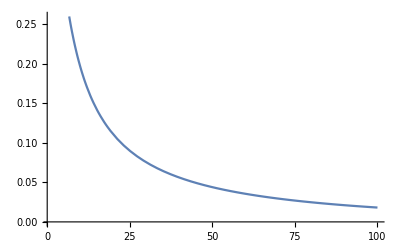

```mathematica
Plot[y[3,B, 1],{B,χ + 0.01,100}]
```

```mathematica
CapitalCashTransferRates=Range[0.8,10,1/4]
```

{0.8,1.05,1.3,1.55,1.8,2.05,2.3,2.55,2.8,3.05,3.3,3.55,3.8,4.05,4.3,4.55,4.8,5.05,5.3,5.55,5.8,6.05,6.3,6.55,6.8,7.05,7.3,7.55,7.8,8.05,8.3,8.55,8.8,9.05,9.3,9.55,9.8}

```mathematica
sol1 := FindRoot[Re[y[1.5,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions1 = B/.sol1
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{421.778,335.367,282.051,245.838,219.616,199.736,184.136,171.562,161.206,152.524,145.139,138.776,133.237,128.369,124.056,120.207,116.75,113.627,110.793,108.207,105.838,103.66,101.65,99.7893,98.0613,96.4521,94.9497,93.5436,92.2248,90.9852,89.8178,88.7162,87.6751,86.6894,85.7547,84.8672,84.0233}

```mathematica
sol2 := FindRoot[Re[y[2,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions2 = B/.sol2
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{389.848,311.293,262.788,229.819,205.928,187.802,173.568,162.087,152.624,144.687,137.929,132.105,127.03,122.568,118.613,115.081,111.907,109.039,106.433,104.056,101.877,99.8719,98.0211,96.3068,94.7142,93.2305,91.8448,90.5474,89.3301,88.1854,87.1069,86.089,85.1266,84.2151,83.3506,82.5294,81.7482}

```mathematica
sol3 := FindRoot[Re[y[3,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions3 = B/.sol3
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{348.428,280.088,237.833,209.074,188.205,172.352,159.888,149.822,141.516,134.541,128.596,123.467,118.994,115.057,111.563,108.441,105.633,103.093,100.784,98.6752,96.7411,94.9604,93.3153,91.7905,90.373,89.0515,87.8165,86.6596,85.5734,84.5514,83.588,82.6782,81.8176,81.002,80.2281,79.4927,78.7928}

```mathematica
sol4 := FindRoot[Re[y[4,B, #]], {B,  χ + 0.01,  χ + 0.01, 100000000}]&/@CapitalCashTransferRates
solutions4 = B/.sol4
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{321.363,259.709,221.541,195.532,176.638,162.268,150.958,141.815,134.263,127.914,122.5,117.823,113.742,110.146,106.954,104.098,101.528,99.2025,97.0866,95.153,93.3785,91.7438,90.2327,88.8314,87.5279,86.3123,85.1756,84.1102,83.1095,82.1676,81.2793,80.44,79.6458,78.8929,78.1781,77.4986,76.8517}

```mathematica
(*We can also produce Figure 7 (a) directly in Mathematica but in our case, to keep the same format, we are going to export the data points and we are going to import them to R: TrappingProbabilityAnalysisBvsct.R.*)
```

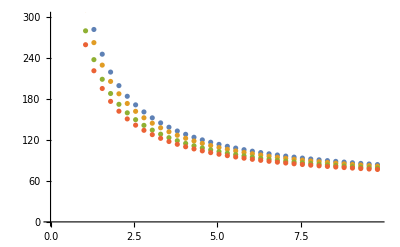

```mathematica
data1=Transpose@{CapitalCashTransferRates,solutions1};
data2=Transpose@{CapitalCashTransferRates,solutions2};
data3=Transpose@{CapitalCashTransferRates,solutions3};
data4=Transpose@{CapitalCashTransferRates,solutions4};
ListPlot[{data1,data2, data3, data4}]
```